## Мухамадиев Владимир

# Задание 5

## Загрузка и предварительная обработка

```mathematica
data1=Import[NotebookDirectory[]<>"\\bio-diseasome.txt","Data"];
```

```mathematica
el1=Table[data1⟦i,1⟧<->data1⟦i,2⟧,{i,1,Length[data1]}];
```

```mathematica
g1=Graph[el1];
```

```mathematica
MeanShortestPath[g_]:=N[Total[Flatten[GraphDistanceMatrix[g]]]/(VertexCount[g]^2-VertexCount[g])]
```

## 1. Конфигурационная модель сетей со степенным распределением

### Генерирует граф в виде списка ребер по заданным степеням вершин

```mathematica
EdgeListByDegreeDistribution[dist_]:=If[Mod[Total[dist],2]==0,Module[{in=dist,vl=Range[Length[dist]],out=ConstantArray[{},Total[dist]/2],temp={{},{}}},Do[Do[temp⟦j⟧=RandomChoice[vl];While[in⟦temp⟦j⟧⟧==0,temp⟦j⟧=RandomChoice[in->vl]];in⟦temp⟦j⟧⟧=in⟦temp⟦j⟧⟧-1,{j,1,2}];out⟦i⟧=Sort[temp]⟦1⟧<->Sort[temp]⟦2⟧,{i,1,Total[dist]/2}];out],Print["Error: Σ≠2n"]]
```

### Сравнение теоретических и фактических значений характеристик графа

```mathematica
FC1[dist_,g_]:=Grid[{{"Характеристики графа","Теория","Модель"},{"Число мультиребер",N[1/2((Mean[dist^2]-Mean[dist])/Mean[dist])^2],Length[DeleteCases[Normal[Counts[DeleteCases[EdgeList[g],a_<->a_]]],_<->_->1]]},{"Число петель",N[1/2(Mean[dist^2]-Mean[dist])/Mean[dist]],Length[DeleteDuplicates[Cases[EdgeList[g],a_<->a_]]]},{"Коэффициент кластеризации",N[1/Length[dist]((Mean[dist^2]-Mean[dist])^2)/Mean[dist]^3],N[GlobalClusteringCoefficient[g]]}},Dividers->All,Background->{None,{Gray,{White}}},Spacings->{1,1}]
```

### Степенное распределение

#### x_min=1,k=1

```mathematica
pdm1k1=Module[{out=Round[RandomVariate[ParetoDistribution[1,1],10000]]},While[OddQ[Total[out]]==True,out=Round[RandomVariate[ParetoDistribution[1,1],10000]]];out];
```

```mathematica
FC1[pdm1k1,Graph[EdgeListByDegreeDistribution[pdm1k1]]]
```

Характеристики графа | Теория | Модель
Число мультиребер | 1.37858×10^8 | 3676
Число петель | 8302.36 | 38
Коэффициент кластеризации | 2109.92 | 0.0214427

#### x_min=1,k=2

```mathematica
pdm1k2=Module[{out=Round[RandomVariate[ParetoDistribution[1,2],10000]]},While[OddQ[Total[out]]==True,out=Round[RandomVariate[ParetoDistribution[1,2],10000]]];out];
```

```mathematica
FC1[pdm1k2,Graph[EdgeListByDegreeDistribution[pdm1k2]]]
```

Характеристики графа | Теория | Модель
Число мультиребер | 5.50394 | 2
Число петель | 1.65891 | 2
Коэффициент кластеризации | 0.000572016 | 0.00114271

#### x_min=1,k=3

```mathematica
pdm1k3=Module[{out=Round[RandomVariate[ParetoDistribution[1,3],10000]]},While[OddQ[Total[out]]==True,out=Round[RandomVariate[ParetoDistribution[1,3],10000]]];out];
```

```mathematica
FC1[pdm1k3,Graph[EdgeListByDegreeDistribution[pdm1k3]]]
```

Характеристики графа | Теория | Модель
Число мультиребер | 0.417978 | 0
Число петель | 0.457153 | 0
Коэффициент кластеризации | 0.0000594986 | 0.

## 2. Конфигурационная модель сложной сети

```mathematica
Module[{gc=Graph[EdgeListByDegreeDistribution[VertexDegree[g1]]]},Grid[{{"Характеристики графа","Исходный граф","Конфигурационный граф"},{"Глобальный коэффициент кластеризации",N[GlobalClusteringCoefficient[g1]],N[GlobalClusteringCoefficient[gc]]},{"Средний локальный коэффициент кластеризации",N[Mean[LocalClusteringCoefficient[g1]]],N[Mean[LocalClusteringCoefficient[gc]]]},{"Средний кратчайший путь",MeanShortestPath[g1],MeanShortestPath[ConnectedGraphComponents[gc]⟦1⟧]}},Dividers->All,Background->{None,{Gray,{White}}},Spacings->{1,1}]]
```

Характеристики графа | Исходный граф | Конфигурационный граф
Глобальный коэффициент кластеризации | 0.430471 | 0.0276029
Средний локальный коэффициент кластеризации | 0.63583 | 0.0151948
Средний кратчайший путь | 6.50899 | 4.19962

## 3. Алгоритм рандомизации

### Функция которая приводит список ребер к виду, где в каждом ребре v_1<->v_2,v_1≤v_2

```mathematica
EdgeSort[edgelist_]:=Module[{out=edgelist},Do[If[edgelist⟦i,1⟧>edgelist⟦i,2⟧,out⟦i⟧=edgelist⟦i,2⟧<->edgelist⟦i,1⟧],{i,1,Length[edgelist]}];out]
```

### Рандомизация графа которая не создает новых петель и мультиребер

```mathematica
GraphRandomization[g_,n_]:=Module[{el=EdgeSort[EdgeList[g]],eltemp={},vltemp={},temp={{},{}},k=0},Do[temp⟦1⟧=RandomChoice[el](*Выбираем первое ребро/петлю*);eltemp=DeleteCases[el,temp⟦1⟧](*Создаем временную выборку из ребер/петель и удалаем из нее все мультиребра/мультипетли для выбранного ребра/петли*);If[temp⟦1,1⟧==temp⟦1,2⟧,(*Алгоритм выбрал петлю*)eltemp=DeleteCases[eltemp,v_<->v_](*удаляем из временной выбрки все петли*);vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранная петля*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данной петлей*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал петлю которую нельзя изменить, так как до любой вершины из нее можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро*)],(*Алгоритм выбрал ребро*)vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧],Cases[eltemp,temp⟦1,2⟧<->_],Cases[eltemp,_<->temp⟦1,2⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранное ребро*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данным ребром*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал ребро которое нельзя изменить, так как до любой вершины из него можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро/петлю*)]];k=1;While[(el⟦k⟧===temp⟦1⟧)==False,k++];el=Delete[el,k];k=1;While[(el⟦k⟧===temp⟦2⟧)==False,k++];el=Delete[el,k](*Удаляем из списка ребер выбранные*);If[RandomInteger[{1,2}]==1(*Случайно выбираем как переключить ребра и добавляем новые к списку ребер*),AppendTo[el,EdgeSort[{temp⟦1,1⟧<->temp⟦2,1⟧}]⟦1⟧];AppendTo[el,EdgeSort[{temp⟦1,2⟧<->temp⟦2,2⟧}]⟦1⟧],AppendTo[el,EdgeSort[{temp⟦1,1⟧<->temp⟦2,2⟧}]⟦1⟧];AppendTo[el,EdgeSort[{temp⟦1,2⟧<->temp⟦2,1⟧}]⟦1⟧]];Label[end],{i,1,n}];Graph[el]]
```

### Функция которая показывает сколько ребер из изначального графа сохранилось при рандомизации в зависимости от числа шагов

```mathematica
GraphRandomizationEvolution[graph_,steps_]:=Module[{temp=graph,el=EdgeSort[EdgeList[graph]],ec=EdgeCount[graph],out=ConstantArray[{},steps+1]},out⟦1⟧=1;Do[temp=GraphRandomization[temp,1];out⟦l⟧=N[Length[EdgeSort[EdgeList[temp]]∩el]/ec],{l,2,steps+1}];out={Range[0,steps],out}ᵀ;out]
```

```mathematica
data1r=Import[NotebookDirectory[]<>"\\sim1r.m"];(*data1r=GraphRandomizationEvolution[g1,EdgeCount[g1]10];*)
```

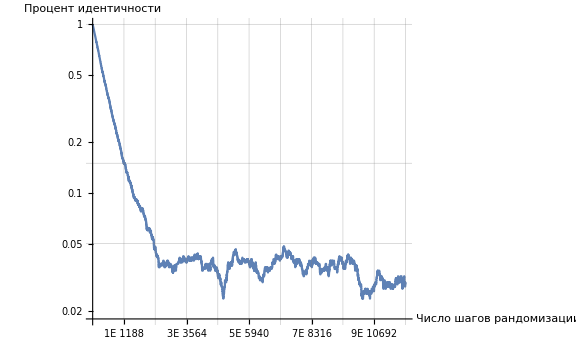

```mathematica
ListLogPlot[data1r,Joined->True,PlotRange->{{0,10EdgeCount[g1]+10},{0,1}},Ticks->{Table[{i EdgeCount[g1],ToString[i]<>"E\n"<>ToString[i EdgeCount[g1]]},{i,1,10}],{{0.05,"5%"},{data1r⟦EdgeCount[g1]+1,2⟧,ToString[NumberForm[100data1r⟦EdgeCount[g1]+1,2⟧,4]]<>"%"},{1,"100%"}}},GridLines->{Table[i EdgeCount[g1],{i,1,10}],{0.05,data1r⟦EdgeCount[g1]+1,2⟧,1}},AxesLabel->{"Число шагов\n рандомизации","Процент\nидентичности"},ImageSize->Large]
```

## 4. Рандомизация сложной сети

### Ансамбль из 100 рандомизированных графов. Число шагов - 10E

```mathematica
g1a=Import[NotebookDirectory[]<>"\\sim1a.m"];(*g1a=Table[GraphRandomization[g1,10EdgeCount[g1]],{l,1,100}];*)
```

```mathematica
Grid[{{"Характеристики графа","Исходный граф","Среднее по ансамблю"},{"Глобальный коэффициент кластеризации",N[GlobalClusteringCoefficient[g1]],N[Mean[Table[GlobalClusteringCoefficient[g1a⟦i⟧],{i,1,100}]]]},{"Средний локальный коэффициент кластеризации",N[Mean[LocalClusteringCoefficient[g1]]],N[Mean[Table[Mean[LocalClusteringCoefficient[g1a⟦i⟧]],{i,1,100}]]]},{"Средний кратчайший путь",MeanShortestPath[g1],Mean[Table[MeanShortestPath[ConnectedGraphComponents[g1a⟦i⟧]⟦1⟧],{i,1,100}]]}},Dividers->All,Background->{None,{Gray,{White}}},Spacings->{1,1}]
```

Характеристики графа | Исходный граф | Среднее по ансамблю
Глобальный коэффициент кластеризации | 0.430471 | 0.0250338
Средний локальный коэффициент кластеризации | 0.63583 | 0.0238955
Средний кратчайший путь | 6.50899 | 3.90221

### Функция которая показывает изменения характеристик графа при рандомизации в зависимости от числа шагов

```mathematica
GraphRandomizationCharacteristicsEvolution[graph_,steps_]:=Module[{temp=graph,gcc=ConstantArray[{},steps+1],mlcc=ConstantArray[{},steps+1],msp=ConstantArray[{},steps+1],out={}},gcc⟦1⟧=N[GlobalClusteringCoefficient[graph]];mlcc⟦1⟧=N[Mean[LocalClusteringCoefficient[graph]]];msp⟦1⟧=MeanShortestPath[ConnectedGraphComponents[graph]⟦1⟧];Do[temp=GraphRandomization[temp,1];gcc⟦l⟧=N[GlobalClusteringCoefficient[temp]];mlcc⟦l⟧=N[Mean[LocalClusteringCoefficient[temp]]];msp⟦l⟧=MeanShortestPath[ConnectedGraphComponents[temp]⟦1⟧],{l,2,steps+1}];out={{Range[0,steps],gcc}ᵀ,{Range[0,steps],mlcc}ᵀ,{Range[0,steps],msp}ᵀ};out]
```

```mathematica
data1cp=Import[NotebookDirectory[]<>"\\sim1cp.m"];(*data1cp=GraphRandomizationCharacteristicsEvolution[g1,EdgeCount[g1]10];*)
```

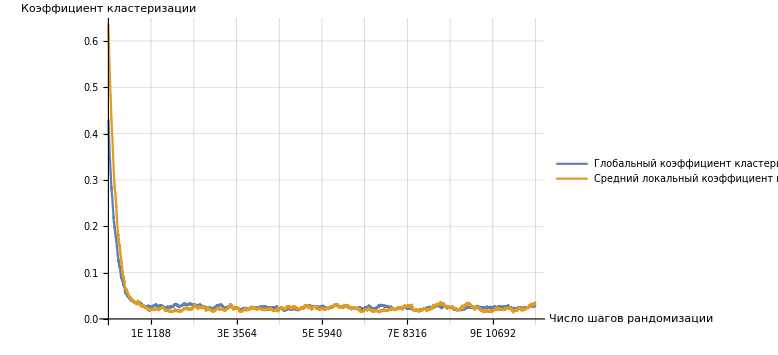

```mathematica
ListLinePlot[data1cp⟦1;;2⟧,PlotRange->{{0,10EdgeCount[g1]+15},All},Ticks->{Table[{i EdgeCount[g1],ToString[i]<>"E\n"<>ToString[i EdgeCount[g1]]},{i,1,10}],Automatic},GridLines->{Table[i EdgeCount[g1],{i,1,10}],Automatic},AxesLabel->{"Число шагов\n рандомизации","Коэффициент\nкластеризации"},PlotLegends->Placed[{"Глобальный коэффициент кластеризации","Средний локальный коэффициент кластеризации"},Below],ImageSize->Large]
```

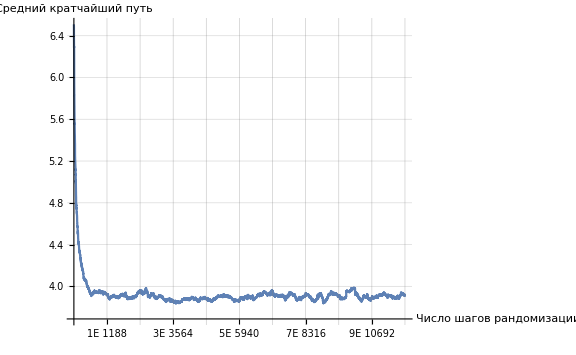

```mathematica
ListLinePlot[data1cp⟦3⟧,PlotRange->{{0,10EdgeCount[g1]+15},All},Ticks->{Table[{i EdgeCount[g1],ToString[i]<>"E\n"<>ToString[i EdgeCount[g1]]},{i,1,10}],Automatic},GridLines->{Table[i EdgeCount[g1],{i,1,10}],Automatic},AxesLabel->{"Число шагов\n рандомизации","Средний\nкратчайший путь"},ImageSize->Large]
```

## 5. Генератор сетей со степенным распределением

### Алгоритм Гавела-Хакими

Алгоритм даёт ответ на вопрос: является ли данная последовательность степеней вершин графической. По графической последовательности возможно построить простой граф.

```mathematica
HavelHakimiAlgorithm[arr_]:=Module[{data=ReverseSort[arr]},If[Evaluate[data∈Integers]==True&&data⟦-1⟧≥0&&data⟦1⟧<Length[data]&&EvenQ[Total[data]]==True,While[data⟦1⟧>0&&data⟦-1⟧≥0,data⟦2;;data⟦1⟧+1⟧-=1;data=ReverseSort[Delete[data,1]]];If[data⟦-1⟧==0,True,False],False]]
```

### Генерирует граф в виде списка ребер по заданным степеням вершин используя алгоритм Гавела-Хакими

```mathematica
HavelHakimiMethod[dist_]:=Module[{in=dist,vl=Range[Length[dist]],out=ConstantArray[{},Total[dist]/2],temp={},temptemp={},vltemp={},intemp={},k=0},While[Evaluate[Total[in]]≠0,temp=RandomChoice[in->vl];temptemp=in⟦temp⟧;in⟦temp⟧=0;intemp=in;vltemp=RandomSample[intemp->vl,temptemp];Do[intemp⟦vltemp⟦j⟧⟧-=1,{j,1,Length[vltemp]}];While[Evaluate[HavelHakimiAlgorithm[intemp]]==False,intemp=in;vltemp=RandomSample[intemp->vl,temptemp];Do[intemp⟦vltemp⟦j⟧⟧-=1,{j,1,Length[vltemp]}]];in=intemp;
Do[k++;out⟦k⟧=temp<->vltemp⟦j⟧,{j,1,Length[vltemp]}]];out]
```

### Пример на графе с мультиребрами и петлями

```mathematica
g2=Graph[{1<->7,2<->3,3<->7,4<->7,4<->9,5<->6,5<->9,5<->9,6<->12,6<->12,7<->12,8<->8,8<->12,8<->13,9<->11,9<->14,10<->10,10<->13,10<->14,10<->14,11<->11,11<->14,11<->14,11<->14,12<->13,12<->13,13<->13,13<->14}]
```

-Graphics-

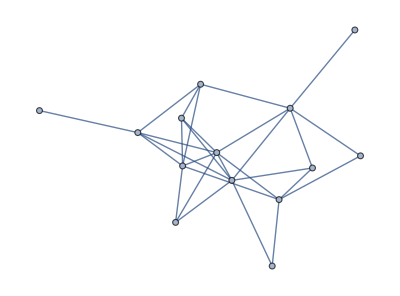

```mathematica
g2r=Graph[HavelHakimiMethod[VertexDegree[g2]]]
```

### Генерация выборки по стпенному распределению по которой возможно построить простой граф

```mathematica
sgs=Module[{out=Round[RandomVariate[ParetoDistribution[1,2],1000]]},While[OddQ[Total[out]]==True||HavelHakimiAlgorithm[out]==False,out=Round[RandomVariate[ParetoDistribution[1,2],1000]]];out];
```

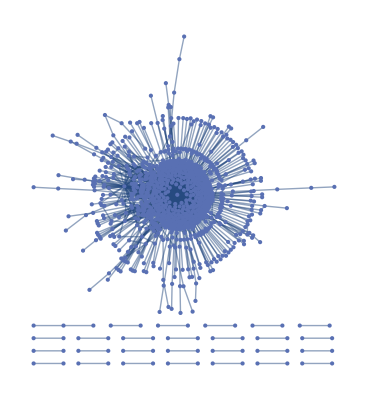

```mathematica
g3=Graph[HavelHakimiMethod[sgs]]
```

### Проверка простоты графа

```mathematica
SimpleGraphQ[g3]
```

True